```mathematica
vertex= {1,2,3,4,5,6,7}
```

{1,2,3,4,5,6,7}

```mathematica
edge={1->7,1->3,2->1,2->5,3->6,3->4,4->7,5->1,5->3,5->4,6->5,7->3,7->5}
```

{1->7,1->3,2->1,2->5,3->6,3->4,4->7,5->1,5->3,5->4,6->5,7->3,7->5}

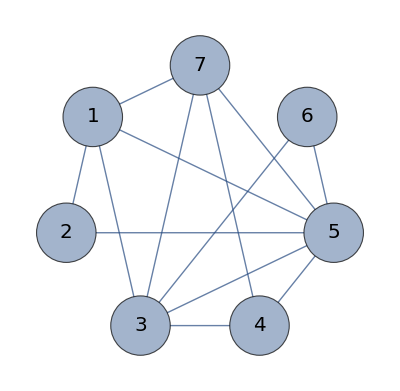

```mathematica
Graph[vertex,edge,VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Black,Italic,20],GraphLayout->"CircularEmbedding",VertexSize->0.5,EdgeShapeFunction->GraphElementData["Arrow","ArrowSize"->0.05]]
```

```mathematica
vertex= {1,2,3,4}
```

{1,2,3,4}

```mathematica
edge={1<->2,2<->3,3<->4,4<->1}
```

{1<->2,2<->3,3<->4,4<->1}

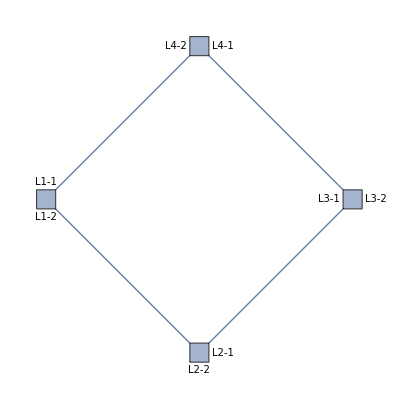

```mathematica
Graph[{Labeled[1,Placed[{"L1-1","L1-2"},{Above,Below}]],Labeled[2,Placed[{"L2-1","L2-2"},{After,Below}]],Labeled[3,Placed[{"L3-1","L3-2"},{Before,After}]],Labeled[4,Placed[{"L4-1","L4-2"},{After,Before}]]},edge,VertexShapeFunction->"Square",VertexLabelStyle->Directive[Black,Italic,10],GraphLayout->"CircularEmbedding",VertexSize->0.1]
```


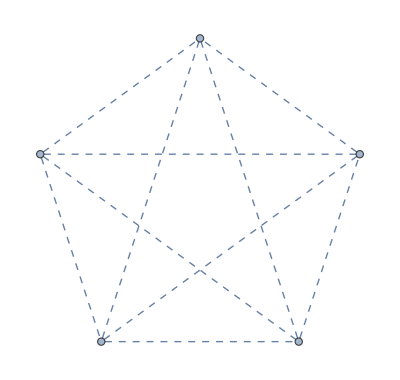
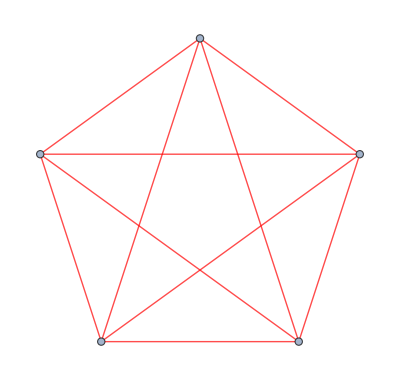

```mathematica
Table[CompleteGraph[5,EdgeStyle->style],{style,{Thick,Dashed,Red}}]
```

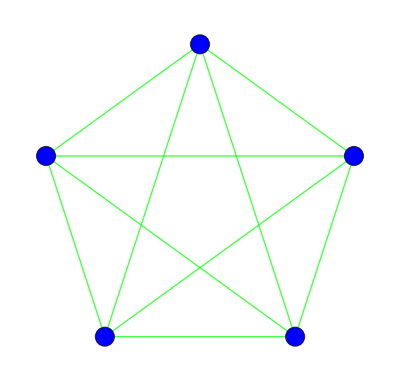
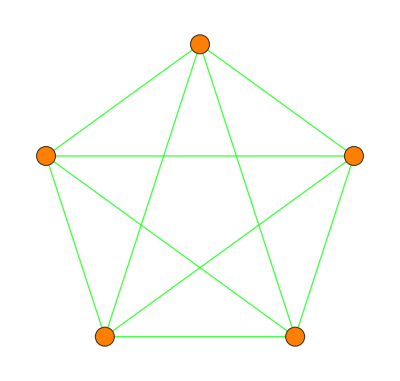
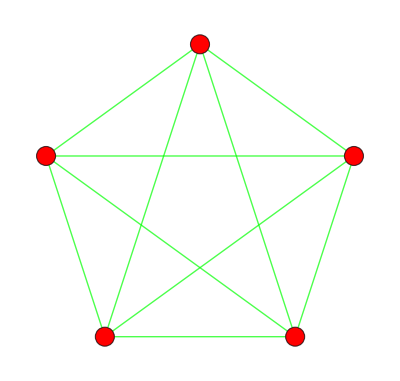

```mathematica
Table[CompleteGraph[5,EdgeStyle->Green,VertexSize->Small,VertexStyle->style],{style,{Blue,Orange,Red}}]
```

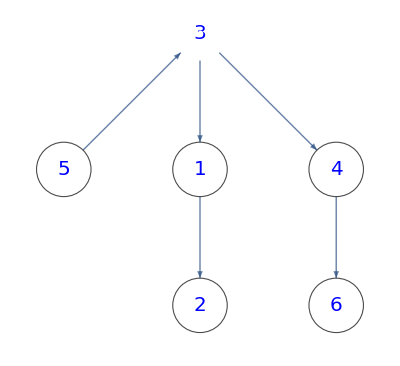

Graph::nonopt: Options expected (instead of Null) beyond position 2 in Graph[{1->2,3->1,3->4,4->6,5->3},VertexSize→Large,Null,VertexStyle→GrayLevel[1],VertexLabels→Placed[Name,Center],VertexLabelStyle→Directive[RGBColor[0, 0, 1],Italic,20],GraphLayout→LayeredEmbedding]. An option must be a rule or a list of rules.

Graph[{1->2,3->1,3->4,4->6,5->3},VertexSize→Large,Null,VertexStyle→GrayLevel[1],VertexLabels→Placed[Name,Center],VertexLabelStyle→Directive[RGBColor[0, 0, 1],Italic,20],GraphLayout→LayeredEmbedding]

```mathematica
Graph[{1->2,3->1,3->4,4->6,5->3},VertexSize->Large,VertexShape->{3->Import["ExampleData/turtle.jpg"]},VertexStyle->White,VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Blue,Italic,20],GraphLayout->"LayeredEmbedding"]
```

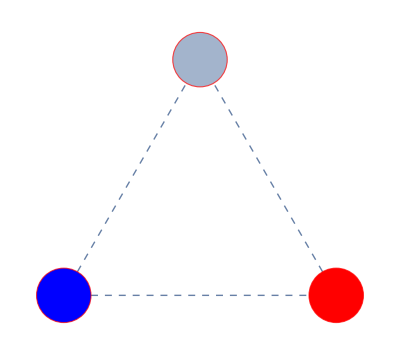
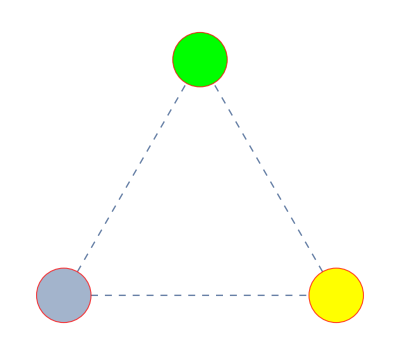
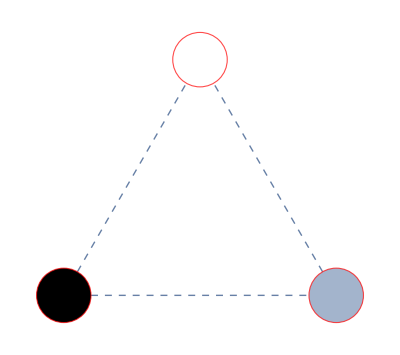

```mathematica
Table[Graph[{1<->2,2<->3,3<->1},VertexStyle->style ,VertexSize->0.2,BaseStyle->EdgeForm[Red],EdgeStyle->Dashed],{style,{{1->Blue,2->Red},{2->Yellow,3->Green},{1->Black,3->White}}}]
```

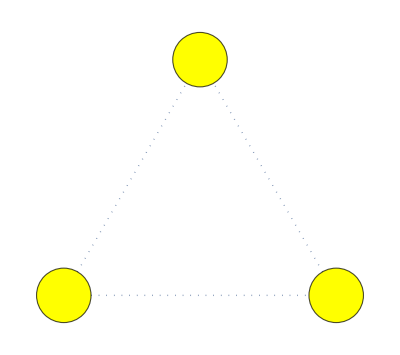
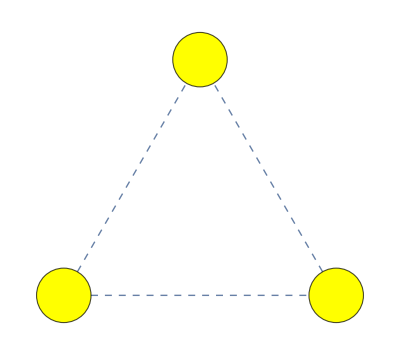
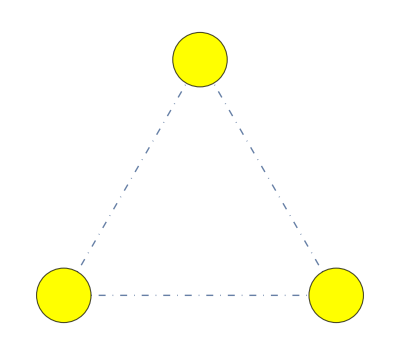

```mathematica
Table[Graph[{1<->2,2<->3,3<->1},VertexStyle->Yellow,BaseStyle->EdgeForm[style],EdgeStyle->style,VertexSize->0.2],{style,{Dotted,Dashed,DotDashed}}]
```

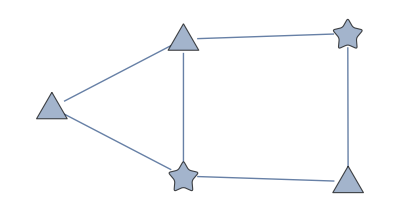

Graph[{1,2,3,4,5},VertexShapeFunction→{EvenQ→ConcavePentagon,OddQ→Triangle},VertexSize→0.2]

```mathematica
Graph[{1,2,3,4,5},{1<->2,1<->4,2<->3,2<->5,3<->5,3<->4},VertexShapeFunction->{ _?EvenQ->
"ConcavePentagon", _?OddQ->"Triangle"},VertexSize->0.2]
```

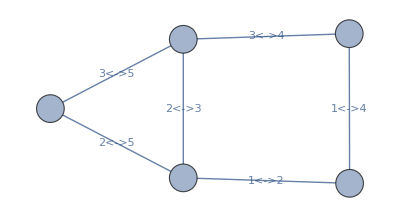

```mathematica
Graph[{1,2,3,4,5},{Labeled[1<->2,"1<->2"],Labeled[1<->4,"1<->4"],Labeled[2<->3,"2<->3"],Labeled[2<->5,"2<->5"],Labeled[3<->5,"3<->5"],Labeled[3<->4,"3<->4"]},VertexShapeFunction->"Circle",VertexSize->0.2]
```

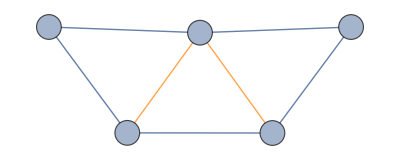

```mathematica
Graph[{1->2,2->3,3->1,3->4,4->1, 4->5, 5->3 },VertexSize->Medium,VertexLabels->Placed["Name", Center], EdgeStyle-> {3->1 -> Orange,3->4 -> Orange},EdgeShapeFunction->GraphElementData["Arrow","ArrowSize"->0.05]]
```

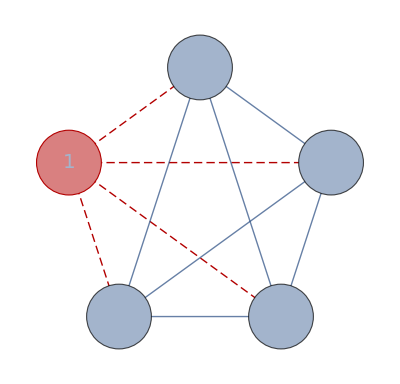

```mathematica
DirectedGraph[CompleteGraph[5, VertexSize-> Large, VertexLabels->Placed["Name", Center], VertexLabelStyle->Directive[Italic,20],EdgeShapeFunction->GraphElementData["Arrow","ArrowSize"->0.05],GraphHighlightStyle->"Dashed",GraphHighlight-> {1,1->2,1->3,1->4,1->5}], "Acyclic"]
```

```mathematica
HighlightGraph[DirectedGraph[CompleteGraph[5, VertexSize-> Large, VertexLabels->Placed["Name", Center], VertexLabelStyle->Directive[Italic,20],EdgeShapeFunction->GraphElementData["Arrow","ArrowSize"->0.05]], "Acyclic"],{1,1->2,1->3,1->4,1->5}, GraphHighlightStyle->"Dashed"]
```

-Graphics-